```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
junctionsEvidenceVsDates=Drop[Import["gi2015.sample_count_submission_date_overlap_geq_20.tsv", "TSV"], 1];
```

```mathematica
(*Convert from days after 2/27/2009 to dates*)
```

```mathematica
daysToDate = DateObject[{2009, 2, 27}]+LinguisticAssistant &
```

Fri 27 Feb 2009+#1&

```mathematica
sortedDays= Sort[Transpose[junctionsEvidenceVsDates][[3]]];
```

```mathematica
(*When were junctions supported by reads in ≥ 20 reads across samples found?*)
```

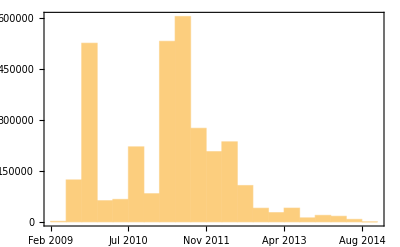

```mathematica
preHist = Histogram[sortedDays, Frame->True, FrameTicks->{{{0,DateString[daysToDate[0], {"MonthNameShort"," ","Year"}]},{500,DateString[daysToDate[500], {"MonthNameShort"," ","Year"}]},{1000,DateString[daysToDate[1000], {"MonthNameShort"," ","Year"}]},
{1500,DateString[daysToDate[1500], {"MonthNameShort"," ","Year"}]},
{2000,DateString[daysToDate[2000], {"MonthNameShort"," ","Year"}]}},Automatic},ImageSize->Full,BaseStyle->{FontName->"Avenir Next", FontSize->40, Bold},FrameTicksStyle->White, Background->None]
```

```mathematica
commons=Commonest[sortedDays,5]
```

{293,298,748,766,865}

```mathematica
junctionsInCommons=Count[sortedDays, #]&/@Commonest[sortedDays,5]
```

{155069,163007,124664,252628,162196}

```mathematica
daysToDate/@Commonest[sortedDays,5]
```

{Thu 17 Dec 2009,Tue 22 Dec 2009,Thu 17 Mar 2011,Mon 4 Apr 2011,Tue 12 Jul 2011}

```mathematica
(*Some of these dates correspond to peaks in the histogram above. Grepping for the submission dates in biosample_tags.tsv gives samples in the following projects:
1. Study of 69 LCLs (2)(Understanding mechanisms underlying human gene expression variation with RNA sequencing, by Pickrell et al.) 17 Dec 2009
2. Study of 41 Coriell cell lines (SRP001563)(Polymorphic cis-and trans-regulation of human gene expression, by Cheung et al.) 22 Dec 2009
3. Illumina bodyMap2 (ERP000546) 17-Mar-2011
4. University of Washington Human Reference Epigenome Mapping Project (SRP001371)(total RNA, fetal tissues, contributed most junctions on a single day (4 April 2011) at 252,628)
5. ENCODE (SRP007461)*)
```

```mathematica
(*How many junctions covered by ≥ 20 reads are there?*)
```

```mathematica
Length[junctionsEvidenceVsDates]
```

3211228

```mathematica
(*Study number of junctions supported by ≥ K samples*)
```

```mathematica
aggregatedJunctionCounts=Drop[Import["gi2015.sample.stats.tsv", "TSV"], 1];
```

```mathematica
totalJunctions = Transpose[Transpose[aggregatedJunctionCounts][[{1,2}]]];annotatedJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,3}]]];exonSkipJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,4}]]];altStartEndJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,5}]]];
novelJunctions=exonSkips=Transpose[Transpose[aggregatedJunctionCounts][[{1,6}]]];
```

```mathematica
(*Steep dropoff: run-level*)
```

```mathematica
ListPlot[totalJunctions, Joined->True,  Filling->Axis,PlotStyle->Thick, PlotRange->{{0, 50},{0,9000000}}, ImageSize->Full,BaseStyle->{FontName->"Avenir Next", FontSize->40}, Frame->True,FrameTicksStyle->White, Prolog->{White,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}]
```

-Graphics-

```mathematica
(*Introduce levels of evidence*)
```

```mathematica
ListPlot[{totalJunctions,annotatedJunctions,Transpose[{Transpose[annotatedJunctions][[1]],Transpose[annotatedJunctions][[2]]+Transpose[exonSkipJunctions][[2]]}], Transpose[{Transpose[annotatedJunctions][[1]],Transpose[annotatedJunctions][[2]]+Transpose[exonSkipJunctions][[2]]+Transpose[altStartEndJunctions][[2]]}]}, Joined->True, PlotRange->{{20, 100},{0,3000000}}, Filling->Axis,  Frame->True,FrameTicksStyle->White, Prolog->{White,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}, ImageSize->Full, BaseStyle->{FontName->"Avenir Next", FontSize->40}]
```

-Graphics-

```mathematica
ListPlot[{totalJunctions,annotatedJunctions,Transpose[{Transpose[annotatedJunctions][[1]],Transpose[annotatedJunctions][[2]]+Transpose[exonSkipJunctions][[2]]}], Transpose[{Transpose[annotatedJunctions][[1]],Transpose[annotatedJunctions][[2]]+Transpose[exonSkipJunctions][[2]]+Transpose[altStartEndJunctions][[2]]}]}, Joined->True, PlotRange->{{100, 9000},{0,1000000}}, Filling->Axis,  Frame->True,FrameTicksStyle->White, Prolog->{White,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}, ImageSize->Full, BaseStyle->{FontName->"Avenir Next", FontSize->40}]
```

-Graphics-

```mathematica
GTAGJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,7}]]];
annotatedGTAGJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,8}]]];GCAGJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,9}]]];
annotatedGCAGJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,10}]]];
ATACJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,11}]]];
annotatedATACJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,12}]]];
```

```mathematica
ListPlot[{totalJunctions,GTAGJunctions,Transpose[{Transpose[GTAGJunctions][[1]],Transpose[GTAGJunctions][[2]]+Transpose[GCAGJunctions][[2]]}], Transpose[{Transpose[GTAGJunctions][[1]],Transpose[GTAGJunctions][[2]]+Transpose[GCAGJunctions][[2]]+Transpose[ATACJunctions][[2]]}]}, Joined->True, PlotRange->{{100, 1000},{500000,800000}}, Filling->Axis,  Frame->True,FrameTicksStyle->White, Prolog->{White,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}, ImageSize->Full, BaseStyle->{FontName->"Avenir Next", FontSize->40}]
```

-Graphics-

```mathematica
aggregatedJunctionCounts=Drop[Import["gi2015.project.stats.tsv", "TSV"], 1];
```

```mathematica
totalJunctions = Transpose[Transpose[aggregatedJunctionCounts][[{1,2}]]];annotatedJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,3}]]];exonSkipJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,4}]]];altStartEndJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,5}]]];
novelJunctions=exonSkips=Transpose[Transpose[aggregatedJunctionCounts][[{1,6}]]];
```

```mathematica
(*Steep dropoff: project-level*)
```

```mathematica
ListPlot[totalJunctions, Joined->True,  Filling->Axis,PlotStyle->Thick, PlotRange->{{0, 50},{0,9000000}}, ImageSize->Full,BaseStyle->{FontName->"Avenir Next", FontSize->40}, Frame->True,FrameTicksStyle->White, Prolog->{White,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}]
```

-Graphics-